# 实验习题4

## 工科数学分析——数学实验

## 题1

```mathematica
泰勒公式的误差
```

```mathematica
d0=-1;
While[d0<=1,
a=N[Normal[Series[Cos[x],{x,0,5}]]]/.x->d0;
Print[d0,"    ",a,"     ",N[Cos[d0]],"     ",N[Cos[d0]]-a];d0+=0.4]
```

-1    0.541667     0.540302     -0.00136436

-0.6    0.8254     0.825336     -0.0000643851

-0.2    0.980067     0.980067     -8.88254×10^-8

0.2    0.980067     0.980067     -8.88254×10^-8

0.6    0.8254     0.825336     -0.0000643851

1.    0.541667     0.540302     -0.00136436

```mathematica
观察阶数n对误差的影响
```

```mathematica
n=5;
While[n<=10,
a=N[Normal[Series[Cos[x],{x,0,n}]]/.x->1,17];
Print[n,"  ",a,"  ",N[Cos[1],17],"  ",Cos[1]-a];n+=1;
]
```

5  0.54166666666666667  0.54030230586813972  -0.0013643607985269

6  0.54027777777777778  0.54030230586813972  0.0000245280903619

7  0.54027777777777778  0.54030230586813972  0.0000245280903619

8  0.54030257936507937  0.54030230586813972  -2.734969396×10^-7

9  0.54030257936507937  0.54030230586813972  -2.734969396×10^-7

10  0.54030230379188713  0.54030230586813972  2.0762526×10^-9

```mathematica
根据图形观察泰勒展开的误差
```

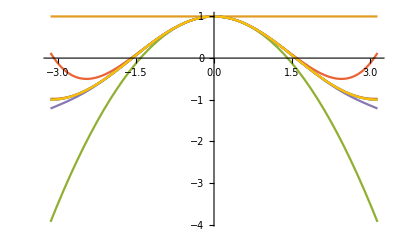

```mathematica
t=Table[Normal[Series[Cos[x],{x,0,i}]],{i,1,13,2}];
PrependTo[t,Cos[x]];
Plot[Evaluate[t],{x,-Pi,Pi}]
```

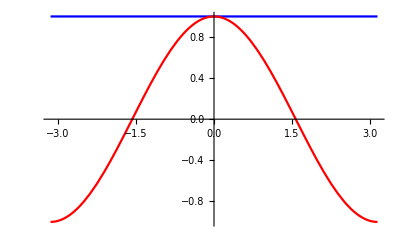

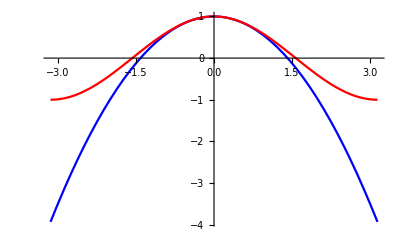

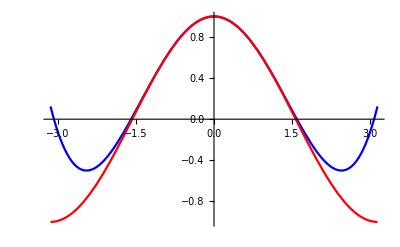

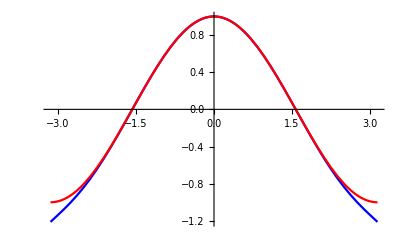

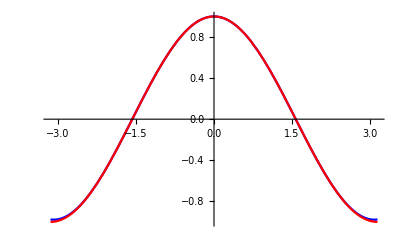

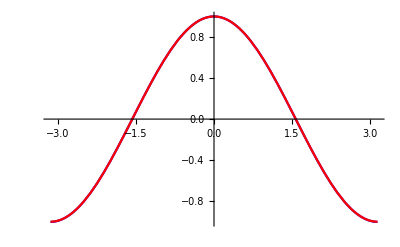

```mathematica
For[i=1,i<=11,a=Normal[Series[Cos[x],{x,0,i}]];
b=Plot[{a,Cos[x]},{x,-Pi,Pi},
PlotStyle->{RGBColor[0,0,1],RGBColor[1,0,0]}];
Print[b];i+=2;
]
```

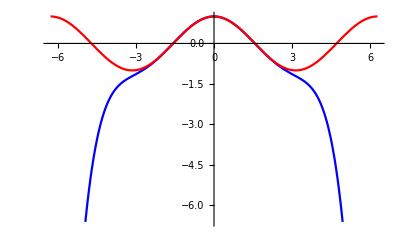

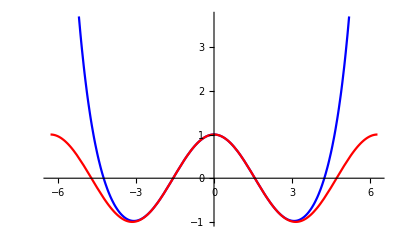

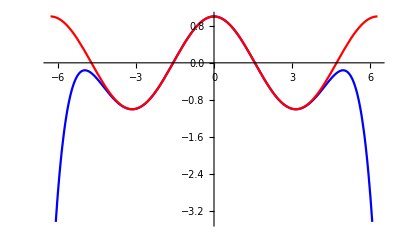

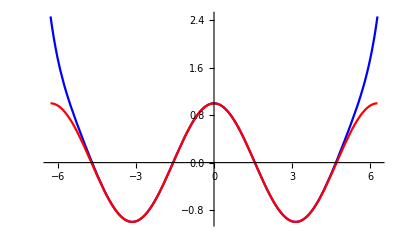

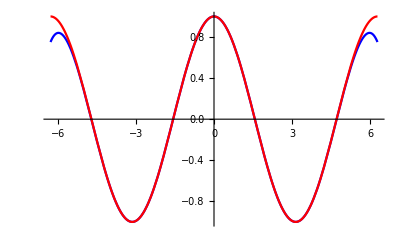

```mathematica
For[i=7,i<=15,a=Normal[Series[Cos[x],{x,0,i}]];
c=Plot[{a,Cos[x]},{x,-2*Pi,2*Pi},
PlotStyle->{RGBColor[0,0,1],RGBColor[1,0,0]}];
Print[c];i+=2;
]
```

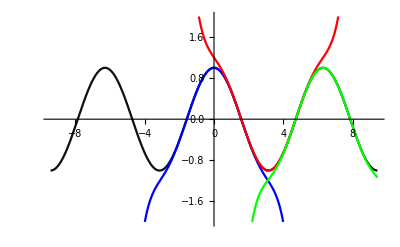

```mathematica
tt[x0_,n_]:=Normal[Series[Cos[x],{x,x0,n}]];
gs0=tt[0,6];gs3=tt[3,6];gs6=tt[6,6];
Plot[{Cos[x],gs0,gs3,gs6},{x,-3*Pi,3*Pi},
PlotRange->{-2,2},PlotStyle->{{RGBColor[0.06,0.06,0.06]},{RGBColor[0,0,1]},{RGBColor[1,0,0]},{RGBColor[0,1,0]}}]
```

## 题2

```mathematica
f[x_]:=Log[Cos[x^2]+Sin[x]];
```

```mathematica
选取阶数依次为1，3，5，7，9，11 的f[x] 在x = 0 处的泰勒展开式函数进行观察
```

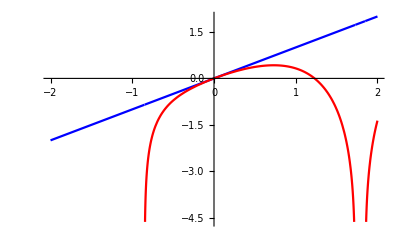

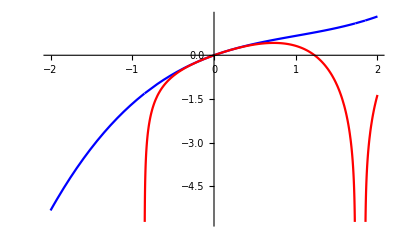

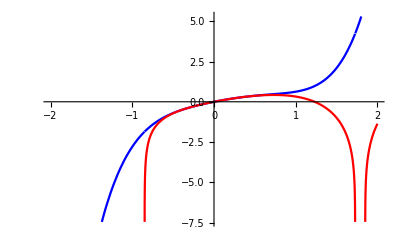

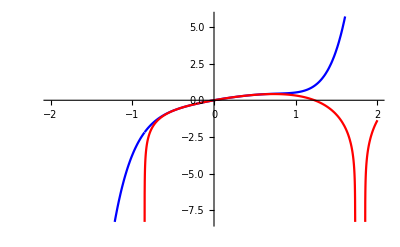

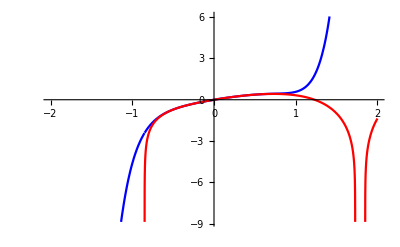

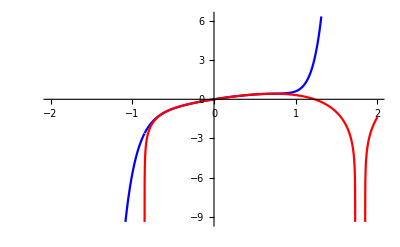

```mathematica
For[i=1,i<=11,a=Normal[Series[f[x],{x,0,i}]];
b=Plot[{a,f[x]},{x,-2,2},
PlotStyle->{RGBColor[0,0,1],RGBColor[1,0,0]}];
Print[b];i+=2;
]
```

```mathematica
选取阶数为6，依次在x = 0，x = 1，x = 2 除的泰勒展开式函数进行观察
```

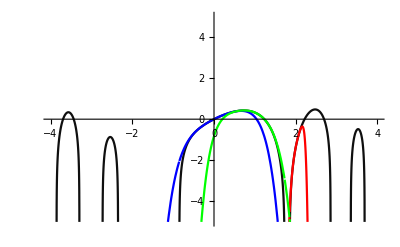

```mathematica
tt[x0_,n_]:=Normal[Series[f[x],{x,x0,n}]];
gs0=tt[0,6];gs3=tt[2,6];gs6=tt[1,6];
Plot[{f[x],gs0,gs3,gs6},{x,-4,4},
PlotRange->{-5,5},PlotStyle->{{RGBColor[0.06,0.06,0.06]},{RGBColor[0,0,1]},{RGBColor[1,0,0]},{RGBColor[0,1,0]}}]
```